```mathematica
(*
	Generates a 2D projection of a hypercube of 'n' dimensions. 
	I really like 3-6, and anything higher looks really cool if you zoom in
*)
```

```mathematica
HyperCube[n_]:=Module[{i,j,l,pointArray,pointAdd,lineArray,gfxList,ang},
pointArray={{0,0}};
lineArray={};
For[i=1,i≤n,i++,
(*Print[i];*)
ang=(i-1)*((2n-2)*Pi/(2n))/(n-1);
(*Print[ang];*)
pointAdd={Cos[Pi/2-ang],Sin[Pi/2-ang]};
(*Print[pointAdd];*)
l=Length[lineArray];
For[j=1,j≤l,j++,
AppendTo[lineArray,{lineArray[[j]][[1]]+pointAdd,lineArray[[j]][[2]]+pointAdd}];
];
l=Length[pointArray];
For[j=1,j≤l,j++,
AppendTo[pointArray,pointArray[[j]]+pointAdd];
AppendTo[lineArray,{pointArray[[j]],pointArray[[j]]+pointAdd}];
(*Print[pointArray];*)
];
];
gfxList={Graphics[Point[pointArray]]};
For[i=1,i≤Length[lineArray],i++,
AppendTo[gfxList,Graphics[Line[lineArray[[i]]]]];
];
Show[gfxList]];
```

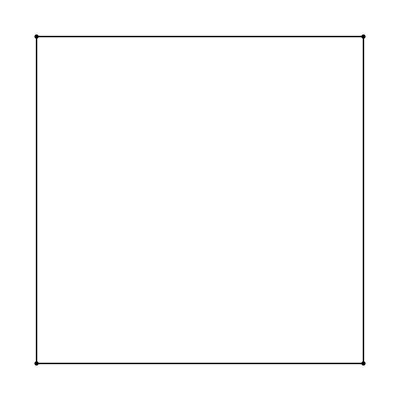

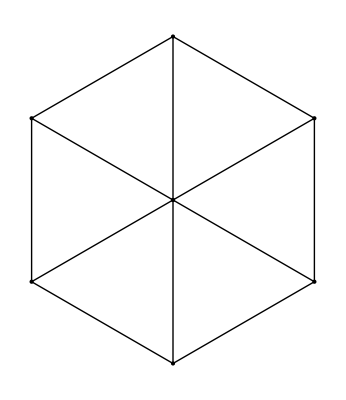

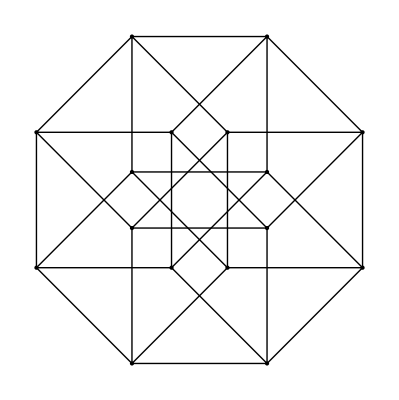

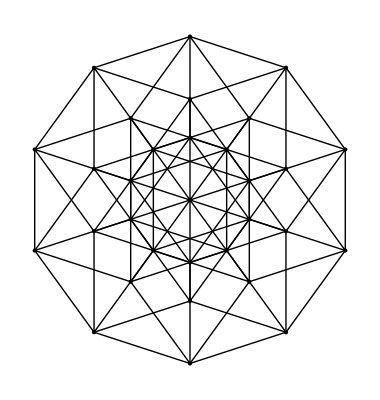

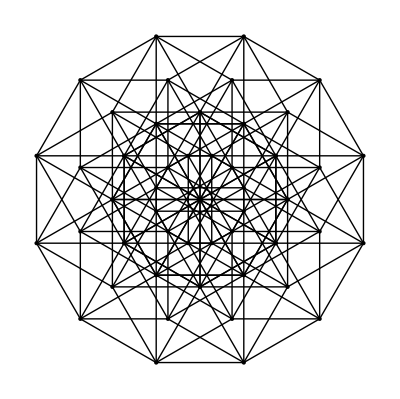

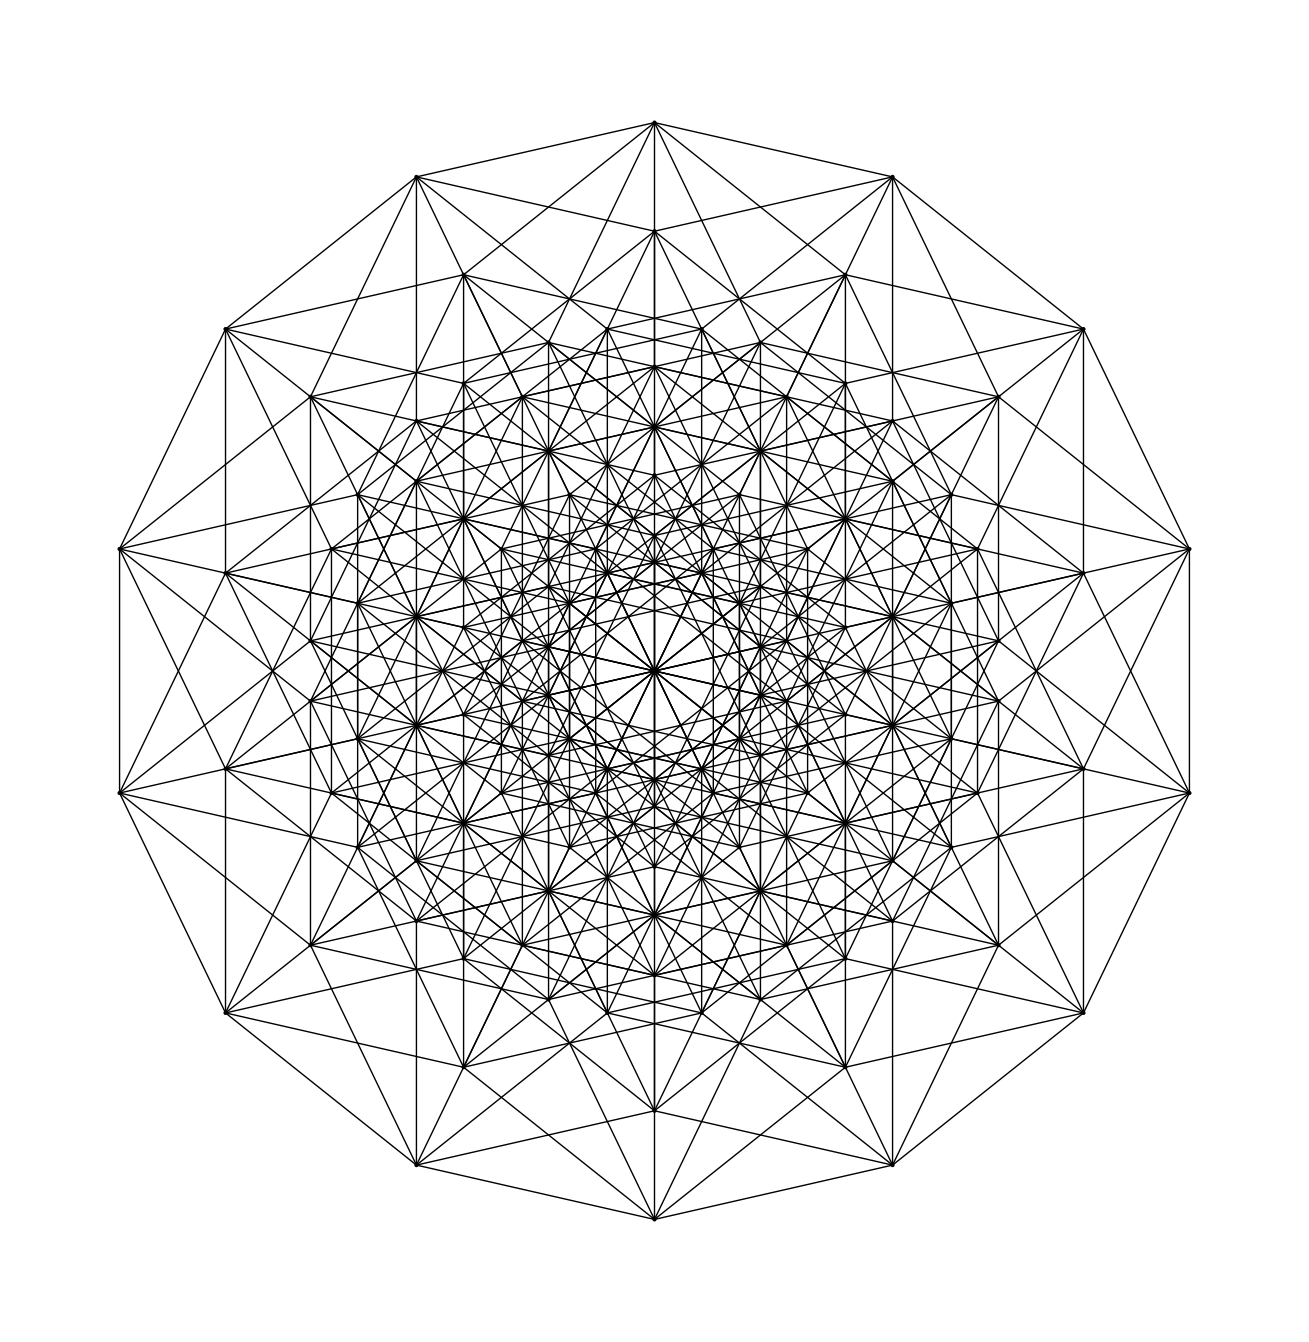

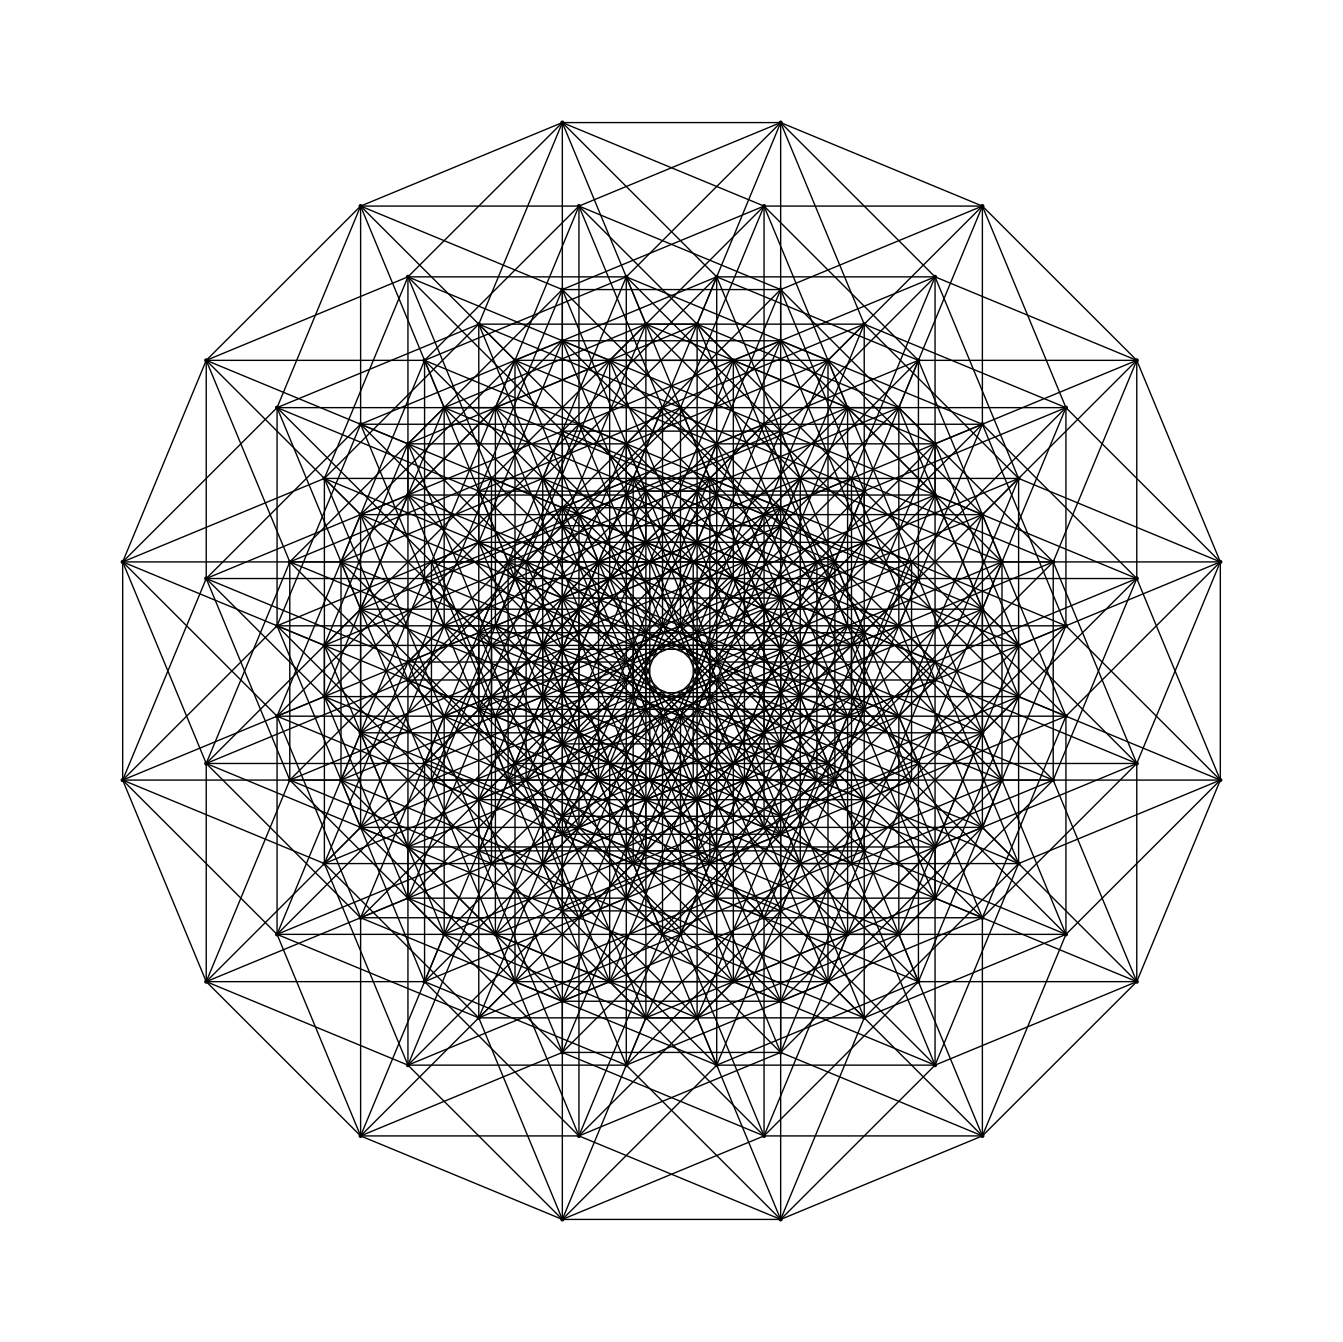

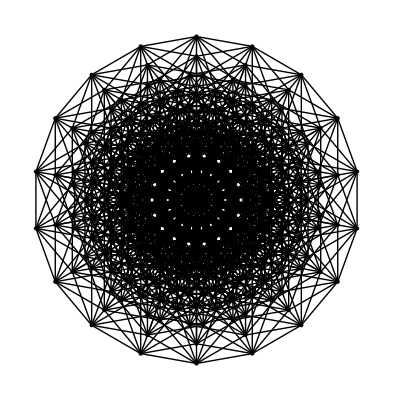

```mathematica
HyperCube[2]
HyperCube[3]
HyperCube[4]
HyperCube[5]
HyperCube[6]
HyperCube[7]
HyperCube[8]
HyperCube[9]
HyperCube[10]
```

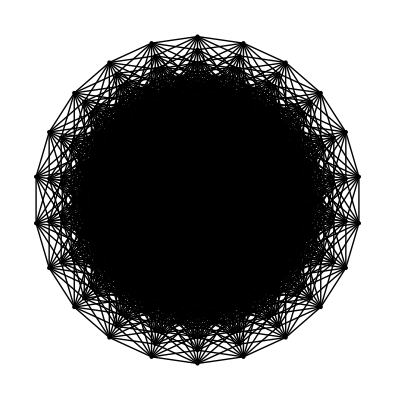

```mathematica
HyperCube[11]
```